```mathematica
MyShow[m_,g_]:=TableForm[{Graph[g,GraphLayout->"CircularEmbedding",ImageSize->150, VertexLabels->"Name"],
Graph[g,GraphLayout->"TutteEmbedding",ImageSize->150, VertexLabels->"Name"],Labeled[TraditionalForm[TableForm[Map[Map[TraditionalForm[#]&,#]&,m], TableDirections->{Column,Row},TableHeadings->{{1<->2,1<->3,1<->4,1<->5,1<->6,2<->4,2<->5,2<->6,3<->5,3<->6,4<->6,5<->6},{"=","≠"}}]],Style[TraditionalForm[FullSimplify[m[[1,1]]+m[[1,2]]]],Red,Bold]]},TableDirections->Row]
```

```mathematica
ContractGraph[g_,e_]:=Graph[Select[VertexList[g],#≠e[[2]]&], With[{k=VertexContract[g,{e[[1]],e[[2]]}]},Print[VertexCount[k]];EdgeList[k]],VertexLabels->{e[[1]]->{e}}]
```

```mathematica
gstart:=Graph[{1,2,3,4,5,6},{2<->3,3<->4,4<->5}]
```

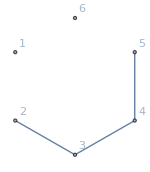
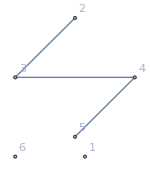
-Graphics- | -Graphics- |  | = | ≠
1<->2 | a | z-a
1<->3 | b | z-b
1<->4 | c | z-c
1<->5 | d | z-d
1<->6 | e | z-e
2<->4 | f | z-f
2<->5 | g | z-g
2<->6 | h | z-h
3<->5 | i | z-i
3<->6 | j | z-j
4<->6 | k | z-k
5<->6 | l | z-lz

```mathematica
start:={{a,z-a},{b,z-b},{c,z-c},{d,z-d},{e,z-e},{f,z-f},{g,z-g},{h,z-h},{i,z-i},{j,z-j},{k,z-k},{l,z-l}};MyShow[start,gstart]
```

5

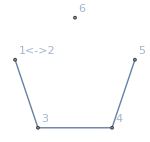
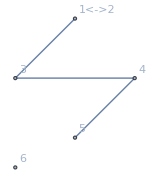
-Graphics- | -Graphics- |  | = | ≠
1<->2 | a | 0
1<->3 | 0 | a
1<->4 | c1 | a-c1
1<->5 | d1 | a-d1
1<->6 | e1 | a-e1
2<->4 | f1 | a-f1
2<->5 | g1 | a-g1
2<->6 | h1 | a-h1
3<->5 | i1 | z-i1
3<->6 | j1 | z-j1
4<->6 | k1 | z-k1
5<->6 | l1 | z-l1a

```mathematica
startContractOneTwo:={{a,0},{0,a},{c1,a-c1},{d1,a-d1},{e1,a-e1},{f1,a-f1},{g1,a-g1},{h1,a-h1},{i1,z-i1},{j1,z-j1},{k1,z-k1},{l1,z-l1}};
gstartContractOneTwo:=ContractGraph[gstart,1<->2];MyShow[startContractOneTwo,gstartContractOneTwo]
```

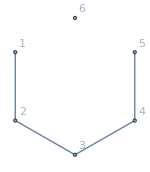
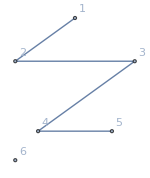
-Graphics- | -Graphics- |  | = | ≠
1<->2 | 0 | z-a
1<->3 | b | -a-b+z
1<->4 | c-c1 | -a-c+c1+z
1<->5 | d-d1 | -a-d+d1+z
1<->6 | e-e1 | -a-e+e1+z
2<->4 | f-f1 | -a-f+f1+z
2<->5 | g-g1 | -a-g+g1+z
2<->6 | h-h1 | -a-h+h1+z
3<->5 | i-i1 | i1-i
3<->6 | j-j1 | j1-j
4<->6 | k-k1 | k1-k
5<->6 | l-l1 | l1-lz-a

```mathematica
startConnectOneTwo:=start-startContractOneTwo;
gstartConnectOneTwo:=EdgeAdd[gstart,1<->2];MyShow[startConnectOneTwo,gstartConnectOneTwo]
```

5

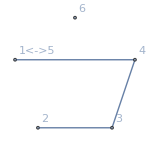
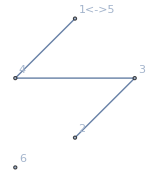
-Graphics- | -Graphics- |  | = | ≠
1<->2 | d | 0
1<->3 | b2 | d-b2
1<->4 | c2 | d-c2
1<->5 | 0 | d
1<->6 | e2 | a-e2
2<->4 | f2 | a-f2
2<->5 | g2 | a-g2
2<->6 | h2 | a-h2
3<->5 | i2 | z-i2
3<->6 | j2 | z-j2
4<->6 | k2 | z-k2
5<->6 | l2 | z-l2d

```mathematica
startContractOneFive:={{d,0},{b2,d-b2},{c2,d-c2},{0,d},{e2,a-e2},{f2,a-f2},{g2,a-g2},{h2,a-h2},{i2,z-i2},{j2,z-j2},{k2,z-k2},{l2,z-l2}};
gstartContractOneFive:=ContractGraph[gstart,1<->5];MyShow[startContractOneFive,gstartContractOneFive]
```

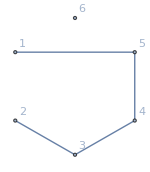
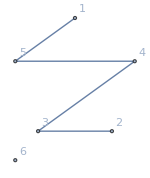
-Graphics- | -Graphics- |  | = | ≠
1<->2 | a-d | z-a
1<->3 | b-b2 | -b+b2-d+z
1<->4 | c-c2 | -c+c2-d+z
1<->5 | d | z-2 d
1<->6 | e-e2 | -a-e+e2+z
2<->4 | f-f2 | -a-f+f2+z
2<->5 | g-g2 | -a-g+g2+z
2<->6 | h-h2 | -a-h+h2+z
3<->5 | i-i2 | i2-i
3<->6 | j-j2 | j2-j
4<->6 | k-k2 | k2-k
5<->6 | l-l2 | l2-lz-d

```mathematica
startConnectOneFive:=start-startContractOneFive;
gstartConnectOneFive:=EdgeAdd[gstart,1<->5];MyShow[startConnectOneFive,gstartConnectOneFive]
```